```mathematica
Resistance = 1000;
Capacitance = 100*10^-9 ;
τ = Resistance *Capacitance
```

1/10000

```mathematica
A[ω_]:=-1/(ⅈ*ω*τ)
```

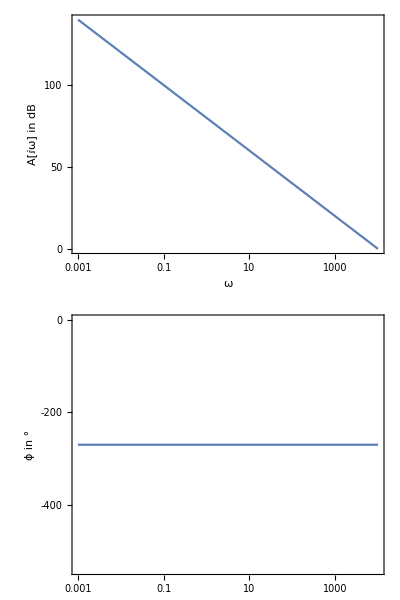

```mathematica
BodePlot[ A[ω],{ω,0.001,10000},ImageSize->Medium, FrameLabel->{{"ω", "A[ⅈω] in dB"},{" ", "ϕ in °"}}]
```